```mathematica
r1=0.0325;
r2=0.0125;
r3=0.003086;
r4=0.0084257;
FHA=7/400;
t=30;
x=r1 t;
R2=r2 t;
R3=r3 t;
R4=r4 t;
Nn=12;
MasterMonth[PV_]:= PV/(Nn t)*((1-r1)((1+FHA)(x/(1-ⅇ^-x))+R4)+R2 +0 )+669/Nn
```

```mathematica
MasterMonth[353036]
```

2174.63

```mathematica
%+73.79
```

2368.4

```mathematica
Qmax=500000;
Qmin=100000;
Npt=40;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
MasterMonthTable=Table[{Q[i],MasterMonth[Q[i]]},{i,0,Npt}];
```

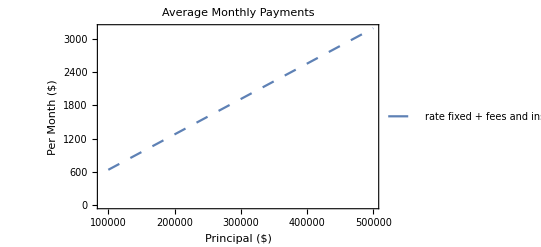

```mathematica
PlotMasterMonth=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"rate fixed + fees and insurance = 0.035"},Frame->True,FrameLabel->{"Principal ($)","Per Month ($)"},PlotLabel->HoldForm["Average Monthly Payments"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
MasterMonthTable
```

(100000 | 638.188
110000 | 702.007
120000 | 765.826
130000 | 829.645
140000 | 893.464
150000 | 957.283
160000 | 1021.1
170000 | 1084.92
180000 | 1148.74
190000 | 1212.56
200000 | 1276.38
210000 | 1340.2
220000 | 1404.01
230000 | 1467.83
240000 | 1531.65
250000 | 1595.47
260000 | 1659.29
270000 | 1723.11
280000 | 1786.93
290000 | 1850.75
300000 | 1914.57
310000 | 1978.38
320000 | 2042.2
330000 | 2106.02
340000 | 2169.84
350000 | 2233.66
360000 | 2297.48
370000 | 2361.3
380000 | 2425.12
390000 | 2488.93
400000 | 2552.75
410000 | 2616.57
420000 | 2680.39
430000 | 2744.21
440000 | 2808.03
450000 | 2871.85
460000 | 2935.67
470000 | 2999.49
480000 | 3063.3
490000 | 3127.12
500000 | 3190.94)

```mathematica
343660/(Nn t)*(x/(1-ⅇ^-x))
```

1541.92

```mathematica
350000/(Nn t)*(r2 t )
```

364.583

```mathematica
350000/(Nn t)*(r3 t )
```

90.0083

```mathematica
350000/(Nn t)*(1-r1)r4 t
```

237.148

```mathematica
359550(1-r1)
```

347865.

```mathematica
%*0.0175
```

5910.63

```mathematica
(1+0.0175)350000(1-r1)
```

343661.

```mathematica
0.07/4
```

0.0175

```mathematica
7/400
```

7/400

```mathematica
N[7/400]
```

0.0175

```mathematica
244/353036
```

61/88259

```mathematica
N[61/88259]
```

0.000691148

```mathematica
586/12
```

293/6

```mathematica
N[293/6]
```

48.8333

```mathematica
r4 is the Property Tax percent
r1 is the Mortgage Rate
r3 is related to Home Owners Insurance
r2  is Mortgage Insurance rate
```